```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20.0*10^3;(*in m/sec*)
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
clight=3 10^8(*m/sec*);
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
mn=12.0;(*in GeV*)
mp=1.0;
tage=3 10^17(*Age in sec*);
n=10^36(*in m^-3*);
rstar=6 10^6(*in m*);
Nn=4/3 π rstar^3 n;
sigmasat=(π rstar^2)/Nn;
βplus[mx_?NumericQ]:=(4 mn  mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn  mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626 10^-34)/(2 π);
pf=hbar (3 π^2 n)^(1/3);
kb=1.38*10^-23(*in J/k*);
rth[mx_,T_]:=((9 kb T)/(4 π G ρ mx 1.78 10^-27))^0.5;
vth[mx_,T_]:=4/3 π rth[mx,T]^3;
```

```mathematica
A=12;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
mup[mx_?NumericQ]:=(mp *mx)/(mp+mx);
```

```mathematica
NchBoson[mdm_]:=1.5 10^34((100(*GeV*))/mdm)^2
```

```mathematica
Tc[Nchi_,gs_]:=(Nchi/(π^3 gs Zeta[3]))^(1/3)(π/3 G ρ)^(1/2)(7.64 10^-12)(*Kelvin*)
TcOld[Nchi_,mdm_,T_,gs_]:=(2π)/mdm((Nchi/vth[mdm,T])/(gs Zeta[1.5]))^(2/3)(23.0)^2/(1.16 10^13)
Nchi0[T_,Nchi_,mdm_,gs_]:=Nchi(1-(T/Tc[Nchi,gs])^3);(*T in Kelvin*)
```

```mathematica
(*WE ASSUME THAT ALL of THE CAPTURED DM has THERMALISED*)
```

```mathematica
NBEC[T_,Nchi_,mdm_,gs_]:=NchBoson[mdm]+Nchi0[T,Nchi,gs]
```

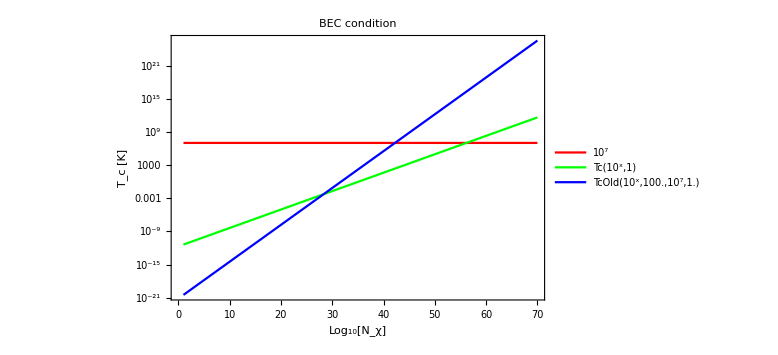

```mathematica
LogPlot[{10^7,Tc[10^x,1],TcOld[10^x,100.,10^7,1.]},{x,1,70},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{0,0},PlotLegends->"Expressions",PlotStyle->{Red,Green,Blue},FrameLabel->{"Log_10[N_χ]","T_c [K]"},PlotLabel->"BEC condition"]
```

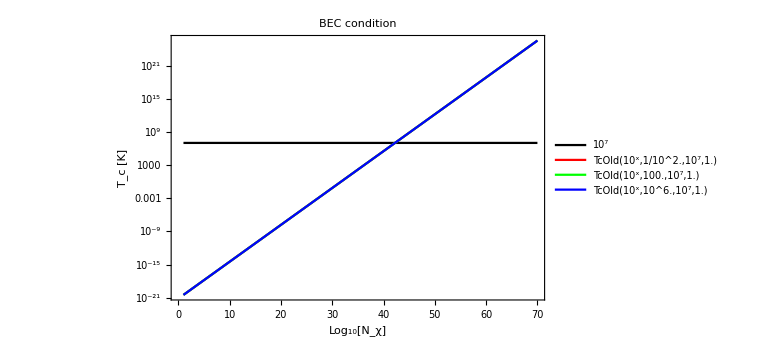

```mathematica
LogPlot[{10^7,TcOld[10^x,10^-2.,10^7,1.],TcOld[10^x,100.,10^7,1.],TcOld[10^x,10^6.,10^7,1.]},{x,1,70},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{0,0},PlotLegends->"Expressions",PlotStyle->{Black,Red,Green,Blue,Orange},FrameLabel->{"Log_10[N_χ]","T_c [K]"},PlotLabel->"BEC condition"]
```

```mathematica
fMBboosted[u_]:=(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2](*Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)*) ;  
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=(vesc^2-u^2)/(vesc^2+u^2)(1+mx^2/mphi^2((u^2+vesc^2)/clight^2))/((1+mx^2/mphi^2(u/clight)^2)(1+mx^2/mphi^2(vesc/clight)^2));
y=vesc/vbar;
Cself[sigmaSelf_,mx_]:=If[y≤ 100,1/3 √(6/π)ρx/mx sigmaSelf vbar(3 y^2+2Exp[-3/2 y^2]-2),1/3 √(6/π)ρx/mx sigmaSelf vbar(3 y^2-2)]
(*Cselfgeneral[sigmaSelf_,mx_,mphi_]:=sigmaSelf ρx/mx NIntegrate[fMBboosted[u]/u(u^2+vesc^2)(g1[u,mx,mphi]),{u,0,vesc}]*)
asq[mx_]:=3/2 vesc^2/vbar^2(4 mx mn)/(mx-mn)^2;
C0[mx_,sigma_]:=If[asq[mx]≤ 100,
(ρx/mx(6/π)^0.5 Min[A^2*mr[mx]^2/mup[mx]^2*sigma,sigmasat]Min[1,δp[mx]/pf]vbar Nn vesc^2/vbar^2(1-(1-Exp[-asq[mx]])/asq[mx])),
(ρx/mx(6/π)^0.5 Min[A^2*mr[mx]^2/mup[mx]^2*sigma,sigmasat] Min[1,δp[mx]/pf]vbar Nn vesc^2/vbar^2(1-1/asq[mx]))];(*With nucleon*)
tsat[sigma_,sigmaSelf_?NumericQ,mx_?NumericQ,T_]:=1/Cself[sigmaSelf,mx] Log[(π (rth[mx,T])^2)/sigmaSelf Cself[sigmaSelf,mx]/C0[mx,sigma]+1.]
```

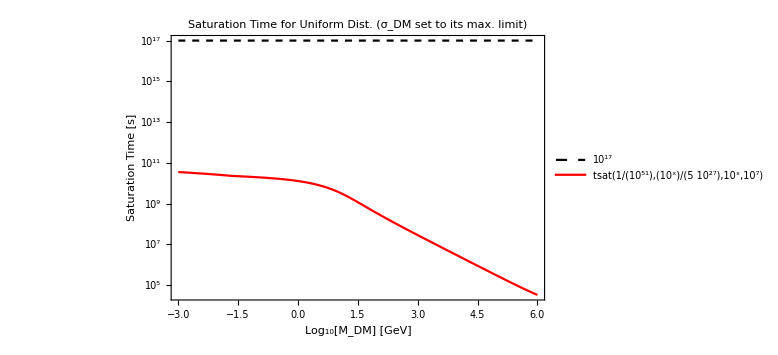

```mathematica
LogPlot[{10^17,tsat[10^-51,10^x/(5 10^27),10^x,10^7]},{x,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist. (σ_DM set to its max. limit)"]

(*tsatGen[sigmaSelf_?NumericQ,mx_?NumericQ,mphi_,T_]:=1/Cselfgeneral[sigmaSelf,mx,mphi] Log[(π (rth[mx,T])^2)/(N0[mx] sigmaSelf)]*)
(*LogPlot[{10^17,tsatGen[10^x/(5 10^27),10^x,0.01,10^7],tsatGen[10^x/(5 10^27),10^x,0.1,10^7],tsatGen[10^x/(5 10^27),10^x,1.,10^7],tsatGen[10^x/(5 10^27),10^x,10^3,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Green,Blue,Orange},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Gen. Dist. (σ_DM set to its max. limit)"]*)
```

```mathematica
Nfinal[sigma_,sigmaSelf_?NumericQ,mx_?NumericQ,T_]:=(Cself[sigmaSelf,mx]/C0[mx,sigma])^-1(Exp[Cself[sigmaSelf,mx]tsat[sigma,sigmaSelf,mx,T]]-1)+(C0[mx,sigma]+π rth[mx,T]^2(1/3 √(6/π)ρx/mx vbar(3 y^2(*+2Exp[-3/2 y^2]*)-2)))(tage-tsat[sigma,sigmaSelf,mx,T])
```

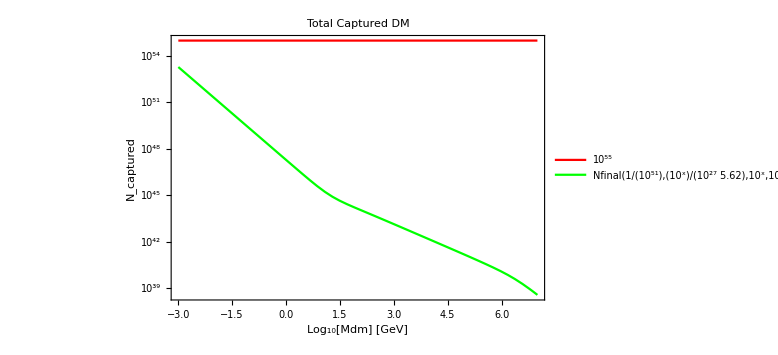

```mathematica
LogPlot[{10^55,Nfinal[10^-51,10^-27/5.62 10^x,10^x,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{Red,Green},FrameLabel->{"Log_10[Mdm] [GeV]","N_captured"},PlotLabel->"Total Captured DM"]
```